{{F→Function[{x,t},(-x-r t λ+r t x λ)/(-1-r t λ+r t x λ)]}}

Piecewise[{{((r t λ)/(1+r t λ))^(-1+m)/(1+r t λ)^2, m≥1}, {-((r t λ)/(1+r t λ))^m/(1+r t λ), 0<m<1}, {(r t λ)/(1+r t λ), m==0}, {0, True}}]

{0.0808824,0.844777,0.0683276,0.00552649,0.000446996,0.0000361541,2.92423×10^-6,2.36518×10^-7,1.91302×10^-8,1.54729×10^-9,1.25149×10^-10,1.01223×10^-11,8.18717×10^-13,6.62197×10^-14,5.35601×10^-15,4.33207×10^-16,3.50388×10^-17,2.83402×10^-18,2.29222×10^-19,1.854×10^-20,1.49956×10^-21,1.21288×10^-22,9.81006×10^-24,7.9346×10^-25,6.4177×10^-26,5.19078×10^-27,4.19843×10^-28,3.39579×10^-29,2.74659×10^-30,2.22151×10^-31,1.79681×10^-32,1.4533×10^-33}

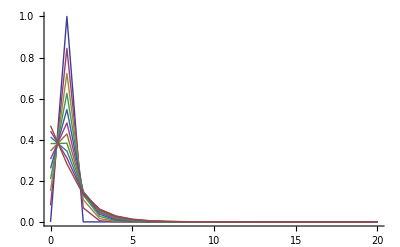

{1,0.977486+0.194375 ⅈ,0.911768+0.377186 ⅈ,0.808004+0.538202 ⅈ,0.67385+0.669554 ⅈ,0.518341+0.766259 ⅈ,0.350779+0.826214 ⅈ,0.179838+0.849804 ⅈ,0.0129989+0.839287 ⅈ,-0.143696+0.798136 ⅈ,-0.28564+0.730474 ⅈ,-0.409499+0.64064 ⅈ,-0.512979+0.532905 ⅈ,-0.594581+0.411319 ⅈ,-0.653378+0.279658 ⅈ,-0.688834+0.141442 ⅈ,-0.70068,-0.688834-0.141442 ⅈ,-0.653378-0.279658 ⅈ,-0.594581-0.411319 ⅈ,-0.512979-0.532905 ⅈ,-0.409499-0.64064 ⅈ,-0.28564-0.730474 ⅈ,-0.143696-0.798136 ⅈ,0.0129989-0.839287 ⅈ,0.179838-0.849804 ⅈ,0.350779-0.826214 ⅈ,0.518341-0.766259 ⅈ,0.67385-0.669554 ⅈ,0.808004-0.538202 ⅈ,0.911768-0.377186 ⅈ,0.977486-0.194375 ⅈ}

{0.0808824,0.844777,0.0683276,0.00552649,0.000446996,0.0000361541,2.92423×10^-6,2.36518×10^-7,1.91302×10^-8,1.54729×10^-9,1.25149×10^-10,1.01224×10^-11,8.18732×10^-13,6.62187×10^-14,5.37036×10^-15,4.7206×10^-16,2.77556×10^-17,-5.55112×10^-17,2.77556×10^-17,1.38778×10^-17,1.2116×10^-17,2.54042×10^-17,1.5582×10^-17,1.58892×10^-17,2.94903×10^-17,0.,2.42861×10^-17,-4.68375×10^-17,-1.92717×10^-17,6.14438×10^-18,3.81345×10^-18,-5.11725×10^-17}

```mathematica
DSolve[{D[F[x,t], t]==λ r (1-x)^2 D[F[x,t], x],F[x,0]==x},F,{x,t}]
FullSimplify[SeriesCoefficient[F[x,t]/.%⟦1⟧,{x,0,m}]]
Table[SeriesCoefficient[F[x,t]/.%%⟦1⟧,{x,0,m}],{m,0,31}] /. {λ->1.1,r->0.08,t->1.0}
ListPlot[Table[Table[{m,SeriesCoefficient[F[x,t]/.%%%⟦1⟧,{x,0,m}]},{m,0,20}] /. {λ->1.1,r->0.08},{t,0,10}],Joined->True,PlotRange->All]
Table[F[R Exp[ⅈ k 2π/32],t],{k,0,31}]//.{λ->1.1,r->0.08,%%%%[[1]][[1]],R->1,t->1.0}
Fourier[%, FourierParameters->{-1,-1}]
```

{{F→Function[{z,t},ⅇ^(-t (λ-z λ))]}}

Piecewise[{{DifferenceRoot[Function[{y,n},{-t λ y[n]+(1+n) y[1+n]==0,y[0]==ⅇ^(-t λ)}]][g], g≥0}, {0, True}}]

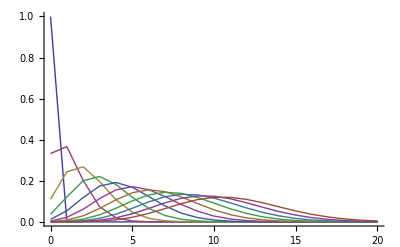

```mathematica
DSolve[{D[F[z,t], t]==(z-1) λ F[z,t],F[z,0]==1},F,{z,t}]
FullSimplify[SeriesCoefficient[F[z,t]/.%⟦1⟧,{z,0,g}]]
ListPlot[Table[Table[{m,SeriesCoefficient[F[z,t]/.%%⟦1⟧,{z,0,m}]},{m,0,20}]/.{λ->1.1} ,{t,0,10}] ,Joined->True,PlotRange->All]
```

```mathematica
DSolve[{D[ξ[τ],τ] == λ (r z (ξ[τ]^2-1) + ξ[τ](1-z)),ξ[t]==x}, ξ,τ]
ξ[0] /. %[[1]] //FullSimplify
Table[SeriesCoefficient[%,{x,0,m},{z,0,g}],{m,0,5},{g,0,5}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ξ→Function[{τ},1/(2 r z)(-1+z+√(-1+2 z-z^2-4 r^2 z^2) Tan[1/2 (√(-1+2 z-z^2-4 r^2 z^2) λ τ+1/(1-2 z+z^2+4 r^2 z^2)√(-1+2 z-z^2-4 r^2 z^2) (-t λ+2 t z λ-t z^2 λ-4 r^2 t z^2 λ-2 √(-1+2 z-z^2-4 r^2 z^2) ArcTan[(-√(-1+2 z-z^2-4 r^2 z^2)+z √(-1+2 z-z^2-4 r^2 z^2)-2 r x z √(-1+2 z-z^2-4 r^2 z^2))/(1-2 z+z^2+4 r^2 z^2)]))])]}}

(-1+z-√(-1-z (-2+z+4 r^2 z)) Tan[1/2 t √(-1-z (-2+z+4 r^2 z)) λ-ArcTan[(1-z+2 r x z)/(√(-1-z (-2+z+4 r^2 z)))]])/(2 r z)

$Aborted

```mathematica
DiscreteFourierTransform
```